{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{0.5,713/1600,10777/25000,17253/40000,17221/40000,21533/50000,86287/200000,85353/200000,17229/40000,43141/100000,86591/200000,86513/200000,5387/12500,43061/100000,86313/200000,86303/200000,21539/50000,2691/6250,85757/200000,21503/50000}

Part::partw: Part 20 of {0,0,0,0,0} does not exist.

{0,0,0,0,0}⟦20⟧

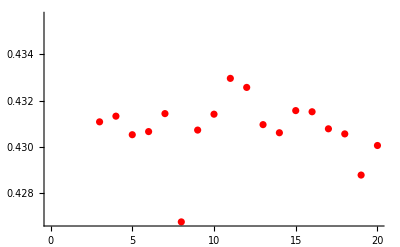

Part::partw: Part 20 of {0,0,0,0,0} does not exist.

{0,0,0,0,0}⟦20⟧

Part::partw: Part 20 of {0,0,0,0,0} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Set::write: Tag Times in Null {0,0,0,0,0}⟦20⟧ is Protected.

```mathematica
m=0.4;
s=0.2;
populationSize=200000;
stepCount=20;
f0=0.5;
tries=5;
fList=Table[0,tries];
For[k=1,k≤tries,k++,
f=Table[0,stepCount];
Print[f];
f[[1]]=f0;
For[k=1,k<stepCount,k++,
f1=m+(1-2*m)*f[[k]];
f2=f1*(1-s)/(1-s*f1);
sampleSize=RandomVariate[BinomialDistribution[populationSize,f2]];
f[[k+1]]=sampleSize/populationSize;
];
Print[f];
Print[fList[[k]]];
Print[Show[ListPlot[Table[{l,f[[l]]},{l,1,stepCount}],PlotStyle->Red]]]; 
f;
Print[fList[[k]]]
fList[[k]]=Table[f[[l]],{l,1,stepCount}];
fList[[k]]];


Manipulate[
withRandomEffect=ListPlot[Table[{l,fList[[k]][[l]]},{l,1,stepCount}],PlotStyle->Red,PlotRange->{{0,stepCount+1},{0,1}},PlotLegends->{"Random effects"},PlotLabel->Style[StringForm["Population count: ``",populationSize],{FontSize->17}],AxesLabel->{Style["n",{FontSize->17}],Style["f[n]",{FontSize->17}]}];
withoutRandomEffect=ListPlot[Table[{l,fList2[[k]][[l]]},{l,1,stepCount}],PlotStyle->Blue,PlotRange->{{0,stepCount+1},{0,1}},PlotLegends->{"No random effects"}];
GraphicsColumn[List[Show[withRandomEffect,withoutRandomEffect]]]
,{k,1,stepCount,1}
]
```

```mathematica
0.4
```

0.4

```mathematica
0.4
```

0.4